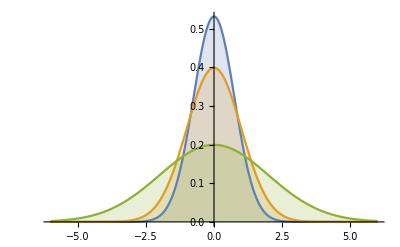

```mathematica
Plot[Evaluate@Table[PDF[NormalDistribution[0,σ],x],{σ,{.75,1,2}}],{x,-6,6},Filling->Axis]
```

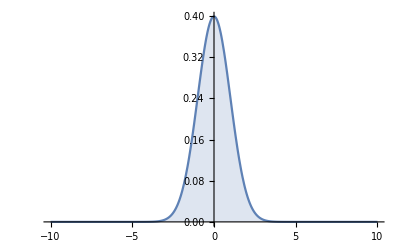

```mathematica
σ=1.0;
Plot[PDF[NormalDistribution[0,σ],x],{x,-10,10},Filling->Axis,PlotRange->Full]
```

```mathematica
Manipulate[Plot[PDF[NormalDistribution[0,σ],x],{x,-10,10},Filling->Axis,PlotRange->{0,0.1}],{σ,0.1,10}]
```

```mathematica
Manipulate[Plot[PDF[VonMisesDistribution[0,σ],x],{x,-π,π},Filling->Axis,PlotRange->{0,2.0}],{σ,0.1,100}]
```

```mathematica
σ = 0.1
sampleSize=10000;
(*randomTable=RandomVariate[NormalDistribution[0,σ],sampleSize];
anglesTable=Map[Function[x,π/2*(1-x)],randomTable];*)
anglesTable=RandomVariate[VonMisesDistribution[0,σ],sampleSize];
normalsTable=Table[{Sin[anglesTable[[i]]],Cos[anglesTable[[i]]]},{i,1,Length[anglesTable]}];
Table[Norm[normalsTable[[i]]],{i,1,Length[normalsTable]}];
averageLength=Sum[normalsTable[[i]][[2]],{i,1,Length[normalsTable]}]/Length[normalsTable]
```

0.1

0.0481934

```mathematica
functionSampleSize = 1000;
f[κ_]:=Sum[Cos[RandomVariate[VonMisesDistribution[0,κ]]],{i,1,functionSampleSize}]/functionSampleSize
```

```mathematica
f[1.0]
```

0.457009

```mathematica
bisou=Table[f[κ],{κ,0.1,100,1}]
```

{0.0664819,0.506442,0.703551,0.805322,0.87788,0.899271,0.909607,0.924141,0.936216,0.942336,0.955233,0.950036,0.954186,0.960438,0.965371,0.96551,0.969364,0.969398,0.972697,0.974429,0.973515,0.975054,0.9767,0.978922,0.980029,0.981044,0.980993,0.982197,0.983155,0.983664,0.984343,0.984228,0.984955,0.985213,0.986267,0.985881,0.986336,0.98576,0.987483,0.986189,0.987245,0.987861,0.988491,0.988437,0.987958,0.989181,0.98791,0.98942,0.989302,0.989582,0.989333,0.989904,0.990985,0.990867,0.990462,0.991244,0.990927,0.990858,0.991639,0.991953,0.991667,0.991469,0.991714,0.991679,0.992239,0.992431,0.992296,0.991982,0.991992,0.992478,0.993452,0.992771,0.992957,0.993111,0.992633,0.99343,0.993469,0.993996,0.993666,0.993256,0.993357,0.994167,0.993616,0.99417,0.99423,0.993597,0.993685,0.99431,0.994107,0.994228,0.994533,0.994547,0.994664,0.994675,0.994685,0.994984,0.994898,0.994632,0.994666,0.995053}

```mathematica
bisou2=Table[f[κ],{κ,0.1,20,1}]
```

{0.0424419,0.507776,0.707798,0.823886,0.870835,0.894034,0.919653,0.927072,0.936193,0.944579,0.949749,0.953902,0.957043,0.961916,0.964586,0.966668,0.969713,0.97211,0.971787,0.974448}

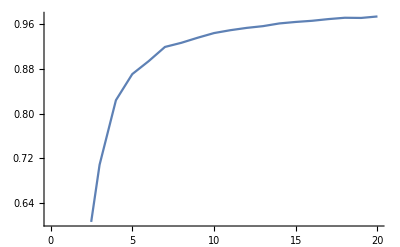

```mathematica
DiscretePlot[bisou2[[i]],{i,1,Length[bisou2]},PlotRange->{-0.1,1},Filling->Axis,ExtentSize->Full];
ListLinePlot[bisou2]
```

```mathematica
(*
 https://www.wolfram.com/mathematica/new-in-8/nonparametric-derived-and-formula-distributions/create-your-own-distribution.html
 *)
```

```mathematica
WrappedNormalPDF[θ_,σ_]:=Sum[Exp[(-(θ+2π k)^2)/(2 σ^2)],{k,-∞,+∞}]/(σ √(2π))
WNDist[σ_]:=ProbabilityDistribution[WrappedNormalPDF[x,σ],{x,-π,+π}]
(*WNDist[σ_]:=ProbabilityDistribution[N[Sum[Exp[(-(θ+2π k)^2)/(2 σ^2)],{k,-∞,+∞}]/(σ √(2π))],{θ,-π,+π}]*
```

```mathematica
WrappedNormalPDF[1,10.0]
```

0.159155

```mathematica
WNDist[1]
```

ProbabilityDistribution[EllipticTheta[3,x/2,1/(√ⅇ)]/(2 π),{x,-π,π}]

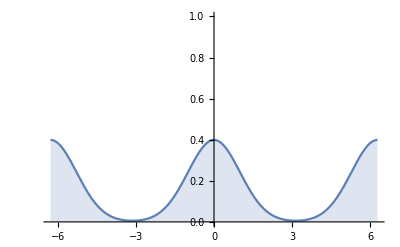

-Graphics-

```mathematica
Plot[WrappedNormalPDF[x,1.0], {x,-2π,2π},Filling->Axis,PlotRange->{0.0,1.0}]
Plot[N[WNDist[1.0]], {x,-π,π},Filling->Axis,PlotRange->Full]
```